Total executions = 752

VWAP market=97.2602

Total volume=95850

VWAP algo=97.2244

Algo traded=8000

Or 8.34637% of total volume

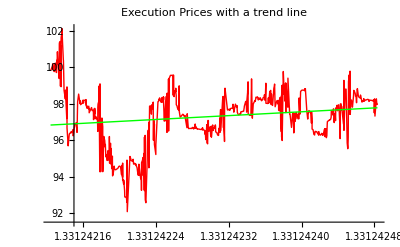

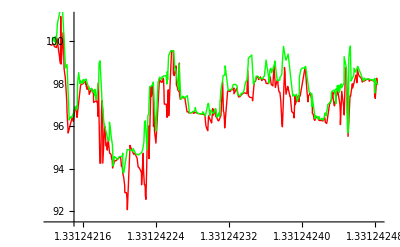

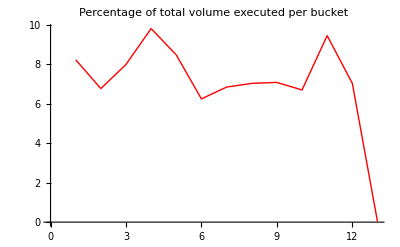

Testing for normal distribution of executed prices

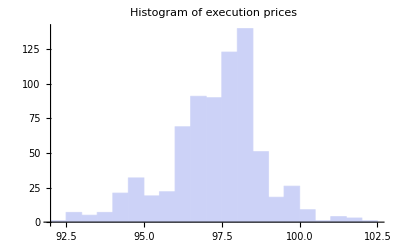

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the "KolmogorovSmirnov" test, which assumes unique values.

Intersection::normal: Nonatomic expression expected at position 2 in {"KolmogorovSmirnov", "Kuiper", "Lilliefors", "WatsonUSquare"} ∩ "KolmogorovSmirnov".

Table::iterb: Iterator {Statistics`GoodnessOfFitTestingDump`i, {"KolmogorovSmirnov", "Kuiper", "Lilliefors", "WatsonUSquare"} ∩ "KolmogorovSmirnov"} does not have appropriate bounds.

The null hypothesis that the data is distributed according to the NormalDistribution[x,y] is rejected at the 5. percent level based on the Kolmogorov-Smirnov test.

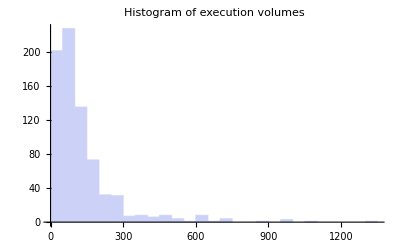

| Statistic | P-Value
Shapiro-Wilk | 0.968122 | 1.28618×10^-11

The null hypothesis that the data is distributed according to the NormalDistribution[x,y] is rejected at the 5. percent level based on the Shapiro-Wilk test.

| Statistic | P-Value
Anderson-Darling | 8.99448 | 5.40027×10^-9

The null hypothesis that the data is distributed according to the NormalDistribution[x,y] is rejected at the 5. percent level based on the Anderson-Darling test.

Import::nffil: File not found during Import.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, executionTimestamp$16600[#1] > start$16600 && newOrderPrice$16600[#1] > 0. &].

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

Function::argb: Function called with 0 arguments; between 1 and 3 arguments are expected.

Testing for normal distribution of new order prices

Histogram::ldata: Function[] is not a valid dataset or list of datasets.

Show::gtype: Histogram is not a type of graphics.

Show[Histogram[Function[]],PlotLabel→Histogram of new order prices]

ShapiroWilkTest::rectuv: The argument Function[] should be a vector or matrix of real numbers with positive variance.

ShapiroWilkTest[Function[],HypothesisTestData][TestDataTable]

ShapiroWilkTest::rectuv: The argument Function[] should be a vector or matrix of real numbers with positive variance.

ShapiroWilkTest[Function[],HypothesisTestData][TestConclusion]

AndersonDarlingTest::rectuv: The argument Function[] should be a vector or matrix of real numbers with positive variance.

AndersonDarlingTest[Function[],Automatic,HypothesisTestData][TestDataTable]

AndersonDarlingTest::rectuv: The argument Function[] should be a vector or matrix of real numbers with positive variance.

General::stop: Further output of AndersonDarlingTest :: rectuv will be suppressed during this calculation.

AndersonDarlingTest[Function[],Automatic,HypothesisTestData][TestConclusion]

```mathematica
ClearAll[report];

report[path_String, buckets_Integer, algoName_String]:=Module[{executionTimestamp, initiatingTrader, restingTrader,side,executionPrice, executionVolume, executionsData, start, stop,executions,executionPricesTimestamps, executionPrices,executionVolumesTimestamps, executionVolumes,executionVolumeTimesPrice,executionsAlgo,executionsAlgoVolumes,executionsAlgoVolumeTimesPrice,executionVolumesBucketed, executionAverageVolumesByBucket,executionPricesLine, newOrderTimestamp, newOrderPrice, newOrderVolume, newOrdersData,newOrders,newOrdersPrices,executionBidsTimestamps,executionAsksTimestamps,executionVolumesTotal},

executionTimestamp = #[[1]]&;
initiatingTrader=#[[2]]&;
restingTrader=#[[5]]&;
side =#[[7]]&;
executionPrice = #[[9]]&;
executionVolume = #[[8]]&;

executionsData = Import[path<> "executions.log"];
start = Min[executionTimestamp[#]&/@executionsData] (*+  filter * 60 * 1000*);
stop = Max[executionTimestamp[#]&/@executionsData];
executions = Sort[Select[executionsData,(* executionTimestamp[#] > start&&*)initiatingTrader[#]≠algoName && restingTrader[#]≠algoName&], OrderedQ[{executionTimestamp[#],executionTimestamp[#2]}]&];
executionPricesTimestamps ={ executionTimestamp[#], executionPrice[#]}&/@executions;
executionPrices = executionPrice[#]&/@executions;
executionVolumesTimestamps={ executionTimestamp[#], executionVolume[#]}&/@executions;
executionVolumes = executionVolume[#]&/@executions;
executionVolumesTotal = executionVolume[#]&/@executionsData;
Print["Total executions = "<>ToString[Length[executionsData]]];

executionVolumeTimesPrice = Total[ executionPrice[#] executionVolume[#]&/@executions];
Print["VWAP market="<>ToString[executionVolumeTimesPrice/Total[executionVolumes]]];
Print["Total volume="<>ToString[Total[executionVolumesTotal]]];

executionsAlgo = Sort[Select[executionsData,(* executionTimestamp[#] > start*)initiatingTrader[#]==algoName || restingTrader[#]==algoName&], OrderedQ[{executionTimestamp[#],executionTimestamp[#2]}]&];
executionsAlgoVolumes = executionVolume[#]&/@executionsAlgo;
executionsAlgoVolumeTimesPrice = Total[ executionPrice[#] executionVolume[#]&/@executionsAlgo];
Print["VWAP algo="<>ToString[executionsAlgoVolumeTimesPrice/Total[executionsAlgoVolumes]]];
Print["Algo traded="<>ToString[Total[executionsAlgoVolumes]]];
Print["Or "<>ToString[N[Total[executionsAlgoVolumes]÷Total[executionVolumesTotal]*100]]<>"% of total volume"];


executionPricesLine = Fit[executionPricesTimestamps, {1,x}, x];
Print[Show[ListLinePlot[executionPricesTimestamps, PlotStyle->Red], Plot[executionPricesLine, {x, start, stop}, PlotStyle->Green], PlotLabel->"Execution Prices with a trend line"]];

executionBidsTimestamps = { executionTimestamp[#], executionPrice[#]}&/@Select[executions,side[#]=="BUY"&];
executionAsksTimestamps = { executionTimestamp[#], executionPrice[#]}&/@Select[executions,side[#]=="SELL"&];
Print[Show[ListLinePlot[executionBidsTimestamps, PlotStyle->Red],ListLinePlot[executionAsksTimestamps, PlotStyle->Green]]];

executionVolumesBucketed =Gather[executionVolumesTimestamps, Quotient[executionTimestamp[#]-start,(stop-start)/buckets]==Quotient[executionTimestamp[#2]-start,(stop-start)/buckets]&] ;
executionAverageVolumesByBucket = Total[Map[#[[2]]&,#]]/Total[executionVolumesTotal ]*100&/@executionVolumesBucketed;
Print[Show[ListLinePlot[executionAverageVolumesByBucket , PlotStyle->Red], PlotLabel->"Percentage of total volume executed per bucket"]];

Print["Testing for normal distribution of executed prices"];
Print[Show[Histogram[executionPrices], PlotLabel->"Histogram of execution prices"]];
Print[KolmogorovSmirnovTest[executionPrices,Automatic,"TestConclusion"]];

Print[Show[Histogram[executionVolumesTotal], PlotLabel->"Histogram of execution volumes"]];

Print[ShapiroWilkTest[executionPrices,"HypothesisTestData"]["TestDataTable"]];
Print[ShapiroWilkTest[executionPrices,"HypothesisTestData"]["TestConclusion"]];
Print[AndersonDarlingTest[executionPrices,Automatic,"HypothesisTestData"]["TestDataTable"]];
Print[AndersonDarlingTest[executionPrices,Automatic,"HypothesisTestData"]["TestConclusion"]];

(*newOrderTimestamp = #[[1]]&;
newOrderPrice = #[[8]]&;
newOrderVolume = #[[7]]&;
newOrdersData = Import[path<> "newOrders.log"];
newOrders = Sort[Select[newOrdersData, executionTimestamp[#] > start && newOrderPrice[#]>0.&], OrderedQ[{newOrderTimestamp[#],newOrderTimestamp[#2]}]&];
newOrdersPrices = newOrderPrice[#]&/@newOrders;

Print["Testing for normal distribution of new order prices"];
Print[Show[Histogram[newOrdersPrices], PlotLabel->"Histogram of new order prices"]];
Print[ShapiroWilkTest[newOrdersPrices,"HypothesisTestData"]["TestDataTable"]];
Print[ShapiroWilkTest[newOrdersPrices,"HypothesisTestData"]["TestConclusion"]];
Print[AndersonDarlingTest[newOrdersPrices,Automatic,"HypothesisTestData"]["TestDataTable"]];
Print[AndersonDarlingTest[newOrdersPrices,Automatic,"HypothesisTestData"]["TestConclusion"]];*)
];

report["/Users/jakubkozlowski/Programming/intellij/eugene/experiment/vwap-no-error/runner/", 12, "VwapAgent12"]
```